```mathematica
Clear["Global`*"]
```

```mathematica
t=Import["C:\\Users\\Samuel\\Dropbox (MIT)\\Grad School Docs\\Shoulders Lab\\2017 08 22 Illumina Sequencing Analysis\\Sam_allele_counts_082217.csv","CSV"];
```

```mathematica
sampleName={"Tight p1d1","Tight p1d2","Tight p1d3","Tight p1d4","Tight p1d5","Tight p1d6","Tight p1d7","Tight p1d8","Tight p1d9","Tight p1d10","Tight p1d11","Tight p1d12","TRE3G p1d0","TRE3G p1d1","TRE3G p1d2","TRE3G p1d3","TRE3G p1d4","TRE3G p1d5","TRE3G p1d6","TRE3G p1d7","TRE3G p1d8","TRE3G p1d9","TRE3G p1d10","TRE3G p1d11","Tight p1d13","NOT Tight p1d14","Dox discrete selection","Dox continuous selection","DBS discrete selection","DBS continuous selection","DBS p1d0","DBS Tight p1d12","DBS TRE3G p1d12"};
```

```mathematica
nonRefFreq=Table[Table[{t[[i+1]][[3]],t[[i+1]][[-1+10*j;;3+10*j]]},{i,1,1750}],{j,1,33}];
```

```mathematica
nonRefFreq[[1]][[500]]
```

{G,0.001343}

```mathematica
nonRefFreqN=Table[Table[t[[i+1]][[3+10*j]],{i,1,1750}],{j,1,33}];
coverageN=Table[Table[t[[i+1]][[-6+10*j]],{i,1,1750}],{j,1,33}];
```

```mathematica
coverageN[[1]][[50]]
```

1189

## Sequencing Coverage

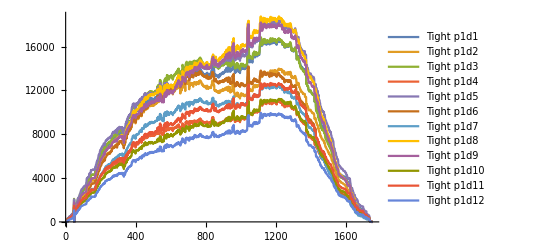

```mathematica
n=1;;12;
ListLinePlot[coverageN[[n]],PlotLegends->sampleName[[n]]]
```

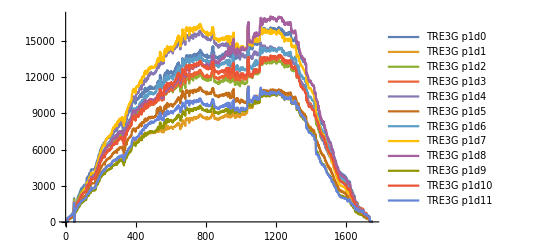

```mathematica
n=13;;24;
ListLinePlot[coverageN[[n]],PlotLegends->sampleName[[n]]]
```

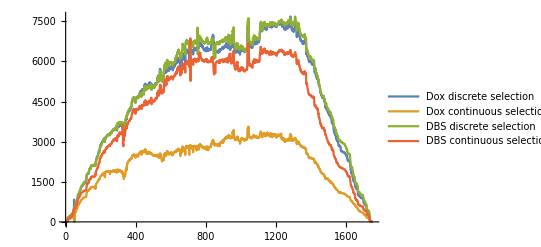

```mathematica
n=27;;30;
ListLinePlot[coverageN[[n]],PlotLegends->sampleName[[n]]]
```

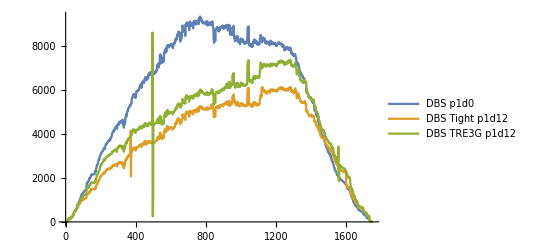

```mathematica
n=31;;33;
ListLinePlot[coverageN[[n]],PlotLegends->sampleName[[n]]]
```

## Non-Reference Mutation Frequency

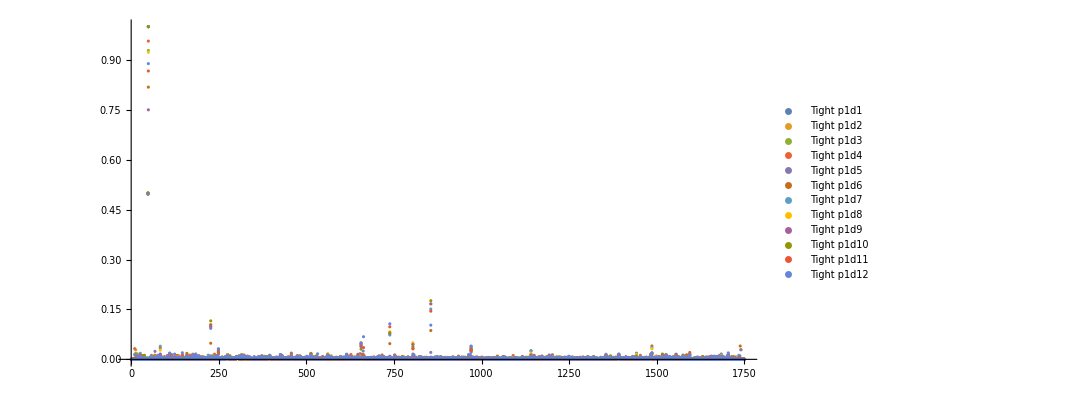

```mathematica
n=1;;12;
ListPlot[nonRefFreqN[[n]],PlotLegends->sampleName[[n]],PlotRange->{0,1},AspectRatio->0.5,ImageSize->800]
```

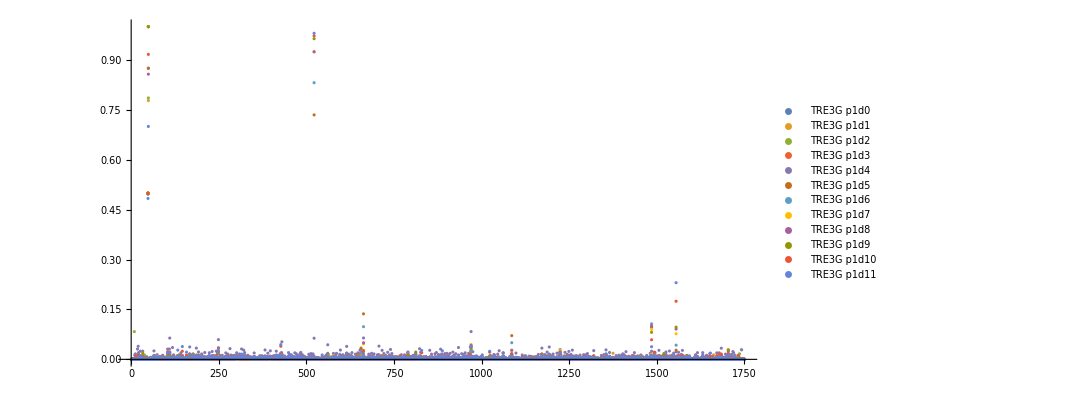

```mathematica
n=13;;24;
ListPlot[nonRefFreqN[[n]],PlotLegends->sampleName[[n]],PlotRange->{0,1},AspectRatio->0.5,ImageSize->800]
```

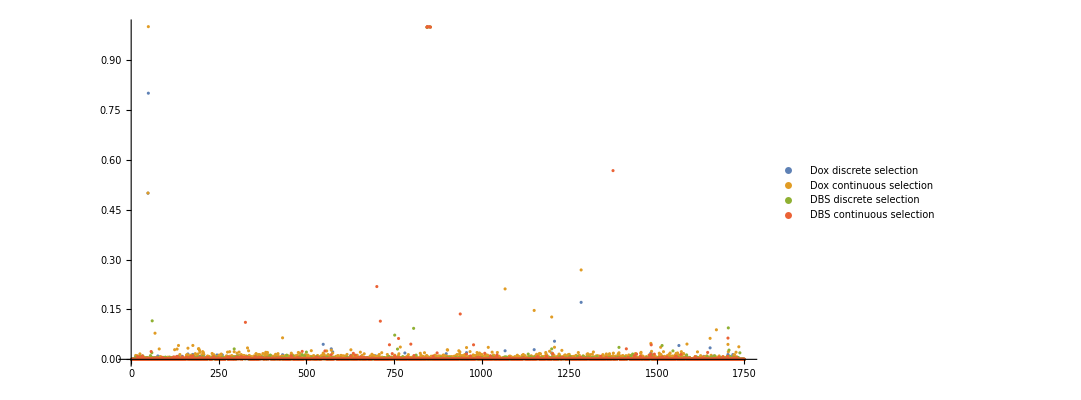

```mathematica
n=27;;30;
ListPlot[nonRefFreqN[[n]],PlotLegends->sampleName[[n]],PlotRange->{0,1},AspectRatio->0.5,ImageSize->800]
```

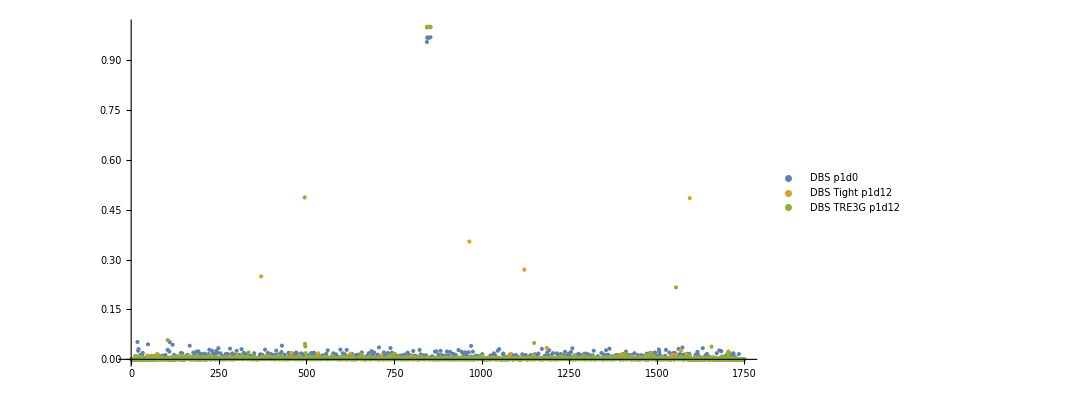

```mathematica
n=31;;33;
ListPlot[nonRefFreqN[[n]],PlotLegends->sampleName[[n]],PlotRange->{0,1},AspectRatio->0.5,ImageSize->800]
```

## Mutations above 5%

```mathematica
mutations={};
For[i=1,i≤Length[nonRefFreqN],i++,
{
AppendTo[mutations,{}];
For[j=51,j≤Length[nonRefFreqN[[i]]],j++,
{If[nonRefFreqN[[i]][[j]]>0.05,AppendTo[mutations[[Length[mutations]]],{j,nonRefFreq[[i]][[j]]}]]}]}]
```

```mathematica
mutations[[10]]//TableForm
```

227 | A |  |  |  | 
0.884366 | 0 | 0.114709 | 0.000925 | 0.115634
738 | A |  |  |  | 
0.919893 | 0.000336 | 0.079436 | 0.000336 | 0.080107
855 | C |  |  |  | 
0.001762 | 0.823769 | 0 | 0.174469 | 0.176231